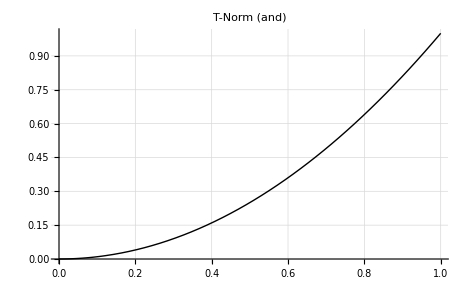

```mathematica
and[x1_, x2_]:=x1*x2
Plot[and[x1,x1],{x1,0,1},
       PlotLabel->Style["T-Norm (and)",FontSize->16],
	GridLines->Automatic,
       PlotStyle->{Thick,GrayLevel[0]}]
```

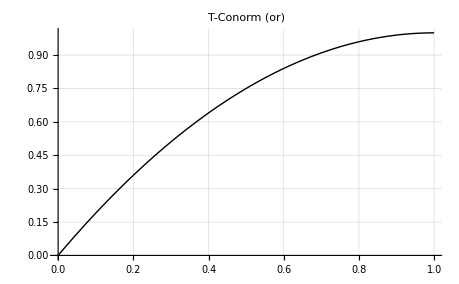

```mathematica
or[x1_, x2_]:=1-(1-x1)*(1-x2)
Plot[or[x1,x1],{x1,0,1},
       PlotLabel->Style["T-Conorm (or)",FontSize->16],
	GridLines->Automatic,
       PlotStyle->{Thick,GrayLevel[0]}]
```